## Checking Validity of Solutions

```mathematica
functionSolve[ldev_,l0_,ϕ_,γ_,δy_,yf_,yDe_,zDe_,yPDe_,zPDe_,tDe_]:=Module[{solutions,seeds,sol,parameters,fulsoly,fulsolz,dsoly,dsolz,sol2,times,ys,tf,tDeU,yDeU,zDeU,yPDeU,zPDeU,yfU,period,Δz,ΔzP},
period=4Pi;
solutions={};
seeds=Table[i,{i,tDe+0.2,tDe+period,0.25}];
leq[t]=l0-ldev Cos[(t-tDe)];
ltri[t]=Sqrt[(y[t]-yf)^2+(z[t])^2];
fk[t]=(leq[t]-ltri[t]);

sol=NDSolve[{ y''[t]==ϕ^2(fk[t])(y[t]-yf)/(ltri[t]),
z''[t]==ϕ^2((fk[t])(z[t])/(ltri[t]))-γ
,y[tDe]==yDe,y'[tDe]==yPDe,z[tDe]==zDe,z'[tDe]==zPDe},{y[t],z[t]},{t,tDe,tDe+period}];

fulsoly=(y[t]/.sol)[[1]];
fulsolz=(z[t]/.sol)[[1]];
dsoly=D[fulsoly,t];
dsolz=D[fulsolz,t];

Do[
sol2=Quiet@FindRoot[dsoly==yPDe,{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
];

times=Select[t/.solutions,(tDe+0.2)<#<(tDe+period)&];
ys=Flatten[(dsoly/.t->times)];
tf=Table[(ys[[i]]-yPDe)<10^-6,{i,1,Length[ys]}];


tDeU=Min[DeleteDuplicates[Pick[times,tf]]];
yDeU=(fulsoly/.t->tDeU);
zDeU=(fulsolz/.t->tDeU);
yPDeU=(dsoly/.t->tDeU);
zPDeU=(dsolz/.t->tDeU);
yfU=yDeU+Abs[δy];

Δz=Abs[Abs[zDe]-Abs[zDeU]];
ΔzP=Abs[Abs[zPDe]-Abs[zPDeU]];

{{yfU,yDeU,zDeU,yPDeU,zPDeU,tDeU},{Δz,ΔzP},{fulsoly,fulsolz,dsoly,dsolz}}

]
```

```mathematica
(*init={0,-0.05,1,0.015,0.008,0}(*Initialize state and first output*);
output=functionSolve[2.4(*ldev*),1.2(*l0*),0.3(*ϕ*),0.00187(*γ*),-0.05(*δy*),0(*yf*),-0.05(*yDe*),1(*zDe*),0.015(*yPDe*),0.008(*zPDe*),0(*tDe*)];
functionSolve[2.4(*ldev*),1.2(*l0*),0.3(*ϕ*),0.00187(*γ*),-0.05,Sequence@@init];*)
```

```mathematica
Module[{ldev=1*1.5,l0=1,ϕ=0.204,γ=0.0041},init={0(*yf*),-0.05(*yDe*),1(*zDe*),0.04(*yPDe*),0(*zPDe*),0(*tDe*)};
output=functionSolve[ldev(*ldev*),l0(*l0*),ϕ(*ϕ*),γ(*γ*),-0.05(*δy*),Sequence@@init];
itration=0;
alloutput={init,output};

(*Loop until condition fails*)
While[Or@@Thread[Abs[output[[2]]]>=10^-7]&&itration<=56,
state=output[[1]];(*Update state*)
output=functionSolve[ldev,l0,ϕ,γ,-0.05,Sequence@@state];
itration++;
result=AppendTo[alloutput,output]];]
```

```mathematica
tiksfunc[xtiks_]:=Module[{mjtiks,mintiks,joined},
mjtiks=Map[{#,#,0.008}&,xtiks];
mintiks=Flatten[Table[Table[{xtiks[[j]]+i(xtiks[[j+1]]-xtiks[[j]])/(3+1),"",0.004},{i,1,3}],{j,1,Length[xtiks]-1}],1];
joined=Join[mjtiks,mintiks];

joined]
```

```mathematica
itration
times=Join[{0},Table[Last[result[[k+1,1]]],{k,1,itration+1}]];
```

57

```mathematica
Needs["MaTeX`"]
```

```mathematica
colors=Flatten[Table[{Directive[RGBColor[0.9,0.6,0.1],Opacity[1]],Directive[RGBColor[0.5,0.1,0.6],Opacity[1]]},itration+1]];
colorslimit=f[Flatten[Table[{times[[k]]<=t<=times[[k+1]],colors[[k]]},{k,1,itration+1}]]];
colorfunction=Which@@(colorslimit/. List->Sequence);
legends=LineLegend[{RGBColor[0.9,0.6,0.1],RGBColor[0.5,0.1,0.6]},{Style["1^st Stance",14],Style["2^nd Stance",14]},LegendMarkerSize->30,LegendLayout->"Row"];
```

```mathematica
yzt=Piecewise[Table[{Flatten[{result[[k+1,3,1]],result[[k+1,3,2]]}],times[[k]]<=t<=times[[k+1]]},{k,1,itration+1}]];
yzplot=ParametricPlot[yzt,{t,First[times],Last[times]},PlotRange->All,Frame->True,LabelStyle->{Black,18,FontFamily->"Latin Modern Roman 10"},FrameLabel->{{"Vertical Position, z",None},{"Forward Position, y",None}},Axes->False,ColorFunction->Function[{x,y,t},Evaluate[colorfunction]],ColorFunctionScaling->False,AspectRatio->0.1,ImageSize->{1000,300},Exclusions->times,FrameTicks->{{tiksfunc[{0.7,0.85,1}],Automatic},{tiksfunc[{0,5,10,15}],Automatic}}]
```

-Graphics-

```mathematica
Length[result]
```

58

```mathematica
footP=Join[{0},Table[First[result[[k+1,1]]],{k,1,itration+1}]];
footPF=Piecewise[Table[{{footP[[k]],0},times[[k]]<=t<=times[[k+1]]},{k,1,itration+1}]];
animie=Manipulate[Show[Graphics[{Thick,(colorfunction/.t->time),Line[{yzt,footPF}/.t->time]},PlotRange->{{14,18.5},{-0.15,result[[itration,1,3]]+0.6}},Frame->True,LabelStyle->{Black,14,FontFamily->"Latin Modern Roman 12"},FrameLabel->{{"Non-dimensional Vertical Position, z",None},{"Non-dimensional Forward Position, y",None}},
Epilog->Text[Style[MaTeX["\\large \\text{$\\varphi=0.0041,$ $\\gamma=0.204,$ $\\delta y=0.05,$ $z_0=1,$ $\\dot{z}_0=0,$ $\\dot{y}_0=0.04,$ $\\ell_\\text{d}=1.5$}"],FontFamily->"Latin Modern Roman 10",Black,13],{16.1,1.3}]
],

ListLinePlot[Table[yzt/.t->tt,{tt,48*2Pi,time,0.01}],PlotStyle->Black],
Graphics[{PointSize[0.025],Black,Point[yzt/.t->time]}],
ImageSize->{800,300}],


{time,Min[times]+48*2Pi,Max[times],0.005,Appearance->"Labeled",ControlPlacement->Top},Bookmarks->{"start":>(time=48*2Pi+10^-6),"end":>(time=Max[times])}]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\Gait.mp4",animie,"AnimationDuration"->10,FrameRate->12]
```

Export::prpchg: Warning: the output frame rate changed from 12 to 10000000/833333.

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\Gait.mp4

```mathematica
N[Max[times]-nt]
Max[times]
```

341.218

373.634

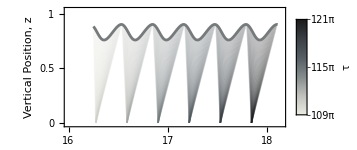

```mathematica
nt=6*2Pi+1;
yzt1=Piecewise[Table[{Flatten[{result[[k+1,3,1]],result[[k+1,3,2]]}],times[[k]]<t<times[[k+1]]},{k,1,itration+1}]];

frames=Table[{Graphics[{Thick,(ColorData["GrayTones",(Max[times]-time)/(nt)]/.t->time),Opacity[0.25],Line[{yzt1,footPF}/.t->time]}],Graphics[{PointSize[0.028],Black,Opacity[0.0],Point[yzt1/.t->time]}]},{time,Max[times]-nt,Max[times],0.25}];

legend=BarLegend[{Function[x,ColorData["GrayTones"][1-x]],{0,1}},LabelStyle->{Black,14,FontFamily->"Latin Modern Math"},LegendLayout->"Column",Ticks->Table[{1-(i-1)/(3-1),ToString[Round[(Max[times]+(i-1)/(3-1)(Max[times]-nt-Max[times]))/Pi,1]]<>ToString[Style["π",FontFamily->"Latin Modern Roman 10"]]},{i,1,3}],LegendMarkerSize->90,LegendLabel->Style["τ",20]];

plot2=Legended[Show[frames,ParametricPlot[yzt,{t,Max[times]-nt,Max[times]},ColorFunction->Function[{x,y,t},ColorData["GrayTones"][1-Rescale[t,{Max[times]-nt,Max[times]}]]],ColorFunctionScaling->False],Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},AspectRatio->0.5,FrameLabel->{{"Vertical Position, z",None},{"Forward Position, y",None}}
,ImageSize->{300,170},PlotRange->{{16,18.14},{-0.015,1.04}},FrameTicks->{{tiksfunc[{0,0.5,1}],Automatic},{tiksfunc[{16,17,18}],Automatic}}],
legend]
```

```mathematica
tiksfunc2[xtiks_]:=Module[{mjtiks,mintiks,joined},
mjtiks=Map[{#,ToString[Round[N[#/Pi],1]]<>ToString[Style["π",FontFamily->"Latin Modern Roman 10"]],0.008}&,xtiks];
mintiks=Flatten[Table[Table[{xtiks[[j]]+i(xtiks[[j+1]]-xtiks[[j]])/(3+1),"",0.004},{i,1,3}],{j,1,Length[xtiks]-1}],1];
joined=Join[mjtiks,mintiks];

joined]
```

```mathematica
speedy=Piecewise[Table[{result[[k+1,3,3]],times[[k]]<=t<=times[[k+1]]},{k,1,itration+1}]];
speedz=Piecewise[Table[{result[[k+1,3,4]],times[[k]]<=t<=times[[k+1]]},{k,1,itration+1}]];
```

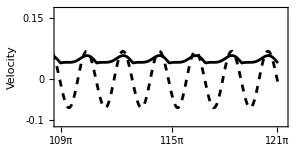

```mathematica
plot1=Plot[{speedy,speedz},{t,First[times],Last[times]},PlotStyle->{{Black},{Black,Dashed}},PlotRange->{{Max[times]-nt-1,Max[times]+1},{-0.11,0.17}},Frame->True,PlotLegends->Placed[LineLegend[Automatic,{MaTeX["\\small \\text{Forward Velocity, }\\dot{y}"],MaTeX["\\small \\text{Vertical Velocity, }\\dot{z}"]},LegendMarkerSize->16,Spacings->0],{0.7,0.84}],LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},Axes->False,FrameLabel->{{"Velocity",None},{"Time, τ",None}},ImageSize->{300,190},FrameTicks->{{tiksfunc[{-0.1,0,0.15}],Automatic},{tiksfunc2[{341,361,380}],Automatic}},AspectRatio->0.5]
```

```mathematica
plot=Show[GraphicsGrid[{{plot2,plot1}},ImageSize->{680,210},Spacings->{Scaled[0.1],Scaled[0]}],
Graphics[{Text[Style["a",18,FontFamily->"Latin Modern Math",Black],{25,10}],
Text[Style["b",18,FontFamily->"Latin Modern Math",Black],{410,10}]
}]

]
```

-Graphics-

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\2DGait.pdf",plot]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\2DGait.pdf

```mathematica
ConfigureMaTeX["pdfLaTeX"->"C:\\Program Files\\MiKTeX\\miktex\\bin\\x64\\lualatex.exe"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{fontspec}\\setmainfont{Latin Modern Math}\\usepackage{amsmath}"}];
```

```mathematica
colors=Flatten[Table[{Directive[RGBColor[0.9,0.6,0.1],Opacity[1]],Directive[RGBColor[0.5,0.1,0.6],Opacity[1]]},itration+1]];
colorslimit=f[Flatten[Table[{times[[k]]<=t<=times[[k+1]],colors[[k]]},{k,1,itration+1}]]];
colorfunction=Which@@(colorslimit/. List->Sequence);
```

```mathematica
speedyz=ParametricPlot[{{t,speedy},{t,speedz}},{t,First[times],Last[times]},PlotStyle->{{Thickness[0.002]},{Dashing[{0.006,0.005}],Thickness[0.002]}},PlotRange->{{0,Max[times]+1},{-0.11,0.19}},Frame->True,PlotLegends->Placed[LineLegend[{Black,Directive[Black,Dashed]},{MaTeX["\\LARGE \\text{Forward Velocity, }\\text{\\LARGE $\\dot{y}$}"],MaTeX["\\LARGE \\text{Vertical Velocity, }\\text{\\LARGE $\\dot{z}$}"]},LegendMarkerSize->30,Spacings->0,LegendLayout->"Row"],{0.7,0.84}],LabelStyle->{Black,18,FontFamily->"Latin Modern Roman 10"},Axes->False,FrameLabel->{{"Velocity",None},{"Time, τ",None}},ImageSize->{1000,150},FrameTicks->{{tiksfunc[{-0.1,0,0.15}],Automatic},{tiksfunc[{0,380/2,380}],Automatic}},AspectRatio->0.1,ColorFunction->Function[{t,x},Evaluate[colorfunction]],ColorFunctionScaling->False]
```

-Graphics-

```mathematica
plot=Show[GraphicsGrid[{{yzplot},{speedyz}},ImageSize->{1100,500},Spacings->{Scaled[0],Scaled[0]}],
Graphics[{Text[Style["a",18,FontFamily->"Latin Modern Math"],{10,-20}],
Text[Style["b",18,FontFamily->"Latin Modern Math"],{10,-250}]

}]
]
```

-Graphics-

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\2DCompleteGait.pdf",plot]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\2DCompleteGait.pdf